## cylindrical nanoscale mosfet compact model -- tunneling current approximation

### physical parameters

```mathematica
e=1.60218 10^-19;(*unit charge[C]*)
kB=1.38066 10^-23;(*Boltzmann constant[J/K]*)h=6.62607 10^-34;(*Planck's constant[Js]*)
hbar=h/(2 π);(*[Js]*)
T=300;(*temperature[K]*)
ϵ0=8.85418 10^-12;(*permittivity in vaccum[F/m]*)vt=(kB T)/e;(*thermal voltage[V]*)
m0=9.10938 10^-31;(*effective mass of electron in vaccum[kg]*)nm=10^-9;
ϵox=3.9 ϵ0;(*permittivity of oxide[F/m]*)
ϵsi=11.8 ϵ0;(*permittivity of silicon according to SILVACO[F/m]*)mt=0.19 m0;(*transverse effective mass of electron in SILICON[kg]*)
ml=0.916 m0;(*longitudinal effective mass of electron in SILICON[kg]*)
mr=2 (ml^-1+mt^-1)^-1;(*effective mass along radius direction in cross section in SILICON[kg]*)
GWF=4.5;(*workfunction of gate material from SILVACO[eV]*)CEA=4.17;(*electron affinity of channel material from SILVACO[eV]*)
wgc=GWF-CEA;(*workfunction difference between gate and channel[V]*)
wfb=0;(*conduction band edge under flat-band condition*)vbi=0.21;(*built-in voltage*)
Eg=0.54;(*fitting parameter*)
```

### device structure parameters

```mathematica
R=2.5 nm;(*radius of cross-section*)
Tox=0.5 nm;(*oxide thickness*)
Cox[r_,tox_]:=2 π (ϵox)/Log[1+tox/r];(*capacitance of cylinder per unit length (F/m)*)
L=9 nm;(*Length of channel*)
```

### bias parameters

```mathematica
VGS0=0;
VGS2=0.2;
VGS5=0.5;
VGS8=0.6;
VDS=0.8;
```

### subbands parameters

```mathematica
besselenergylevel[nf_,nr_,m_,r_]:=hbar^2/(2 m) (BesselJZero[nf,nr]/r)^2
besselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
valleykxky=4;(*4-fold degeneracy*)valleykz=2;(*2-fold degeneracy*)subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,1,mt,R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[0,2,mr,R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,2,mt,R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr,R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[1,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,2,mt,R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[2,2,mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*)
```

{{4,0.19,0.112017,4.333,0.781943,0,0.112017},{2,0.916,0.185548,7.17727,0.781943,0,0.185548},{4,0.19,0.284382,11.0003,0.666667,0,0.284382},{2,0.916,0.471056,18.2212,0.666667,0,0.471056},{4,0.19,0.590213,22.8303,0.688545,0,0.590213},{2,0.916,0.97764,37.8166,0.688545,0,0.97764},{4,0.19,0.953336,36.8765,0.666667,0,0.953336},{2,0.916,1.57913,61.0829,0.666667,0,0.97764},{4,0.19,1.37233,53.0837,0.638438,0,1.37233},{2,0.916,2.27315,87.9289,0.638438,0,2.27315}}

### Fermi Integral

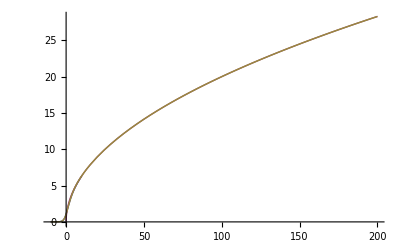

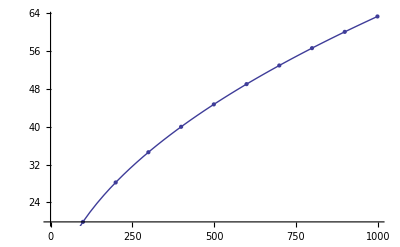

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}]]
```

## potential distribution along channel

### characteristics parameters

```mathematica
γ=Sqrt[4/α]/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2;
ugzero[vbi_,vgs_]:=(vbi-vgs+wgc-wfb)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
ugLg[vbi_,vgs_,vds_]:=(vbi-vgs+wgc-wfb+vds)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
```

### deltaUG along channel

```mathematica
ug[vbi_,vgs_,vds_,z_]:=1/Sinh[γ L] (ugzero[vbi,vgs] Sinh[γ (L-z)]+ugLg[vbi,vgs,vds] Sinh[γ z])
aug[vbi_,vgs_,vds_,z_]:=-(vbi-vgs+wgc-wfb) (Sinh[γ (L-z)]+Sinh[γ z])/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))-vds Sinh[γ z]/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))
Maug[vbi_,vgs_,vds_,z_]:=If[Re[aug[vbi,vgs,vds,z]]≤0,Re[aug[vbi,vgs,vds,z]],0]
```

### potential distribution

```mathematica
ϕ[vbi_,vgs_,vds_,r_,z_]:=WS-ug[vbi,vgs,vds,z] (1-r^2/R^2)/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
```

### the lowest energy level

```mathematica
Eq01[vbi_,vgs_,vds_,z_]:=-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug[vbi,vgs,vds,z]/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
E01[vbi_,vgs_,vds_,z_]:=-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug[vbi,vgs,vds,z]/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
```

### position of barrier top

```mathematica
zmax[vbi_,vgs_,vds_]:=-1/(2 γ) Log[B/A]/.A->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])/.B->ugzero[vbi,vgs]/(2 Sinh[γ L]) Exp[-γ L]+ugLg[vbi,vgs,vds]/(2 Sinh[γ L])
```

### smoothing function

```mathematica
SF[vgs_]:=(1+Exp[μ ((e (vgs-wgc+wfb))/(kB T)-subbandtable[[1,4]]-ν)])^-1/.μ->0.6/.ν->-3
```

### DIBL effect involved deltaUG

```mathematica
DIBLUG[vbi_,vgs_,vds_]:=Re[SF[vgs] Maug[vbi,vgs,vds,zmax[vbi,vgs,vds]]]+U[vgs]
```

## approximation of transit coefficient

### position of the lowest energy of the lowest energy level along channel

```mathematica
zzMAX[vgs_]:=Solve[E01[vbi,vgs,VDS,z]==Eq01[vbi, vgs, VDS, 0],z][[3,1,2]]
zzMAX[VGS0]
FindRoot[E01[vbi,VGS0,VDS,z]==Eq01[vbi, VGS0, VDS, 0],{z,L}][[1,2]]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

7.32582×10^-9

7.91169×10^-9

### equal difference along channel

#### left hand side

```mathematica
deltazLHS[vgs_,vds_,n_]:=zmax[vbi,vgs,vds]/n
deltazLHS[VGS0,VDS,3]
```

1.22974×10^-9

#### right hand side

```mathematica
deltazRHS[vgs_,vds_,n_]:=(zzMAX[vgs]-zmax[vbi,vgs,vds])/n
deltazRHS[VGS0,VDS,3]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

1.2122×10^-9

### rectanglar areasquare approximation for potential distribution

```mathematica
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,deltazLHS[vgs,vds,3]]/;0≤z<=deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,2 deltazLHS[vgs,vds,3]]/;deltazLHS[vgs,vds,3]≤z≤2 deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,3 deltazLHS[vgs,vds,3]]/;2 deltazLHS[vgs,vds,3]≤z≤3 deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,zmax[vbi,vgs,vds]]/;zmax[vbi,vgs,vds]≤z≤zmax[vbi,vgs,vds]+deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,zmax[vbi,vgs,vds]+deltazLHS[vgs,vds,3]]/;zmax[vbi,vgs,vds]+ deltazLHS[vgs,vds,3]≤z≤zmax[vbi,vgs,vds]+2 deltazLHS[vgs,vds,3];
stepE01[vgs_,vds_,z_]:=E01[vbi,vgs,vds,zmax[vbi,vgs,vds]+2 deltazLHS[vgs,vds,3]]/;zmax[vbi,vgs,vds]+2 deltazLHS[vgs,vds,3]≤z≤zmax[vbi,vgs,vds]+3 deltazLHS[vgs,vds,3];
```

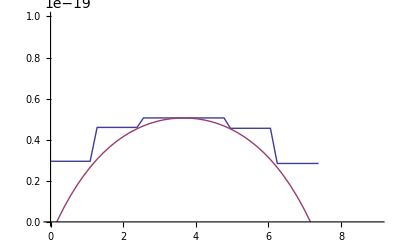

```mathematica
Plot[{stepE01[VGS0,VDS,z],E01[vbi,VGS0,VDS,z],E01[vbi,VGS0,VDS,0]},{z,0,L},PlotRange->{{0,L},{0,1 10^-19}}]
```

## check

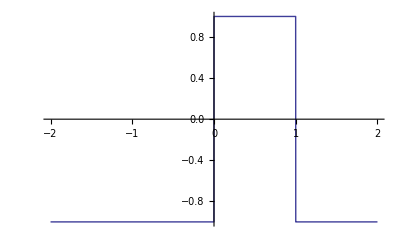

```mathematica
step[x_]:=-1/;x<=0;
step[x_]:=1/;0<=x<=1;
step[x_]:=-1/;1<=x;
Plot[step[x],{x,-2,2}]
```

```mathematica
E01[vbi,VGS0,VDS,zmax[vbi,VGS0,VDS]+2 deltazRHS[VGS0,VDS,3]]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

2.91565×10^-20

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

General::stop: 在本次计算中，Solve :: ifun 的进一步输出将被抑制.

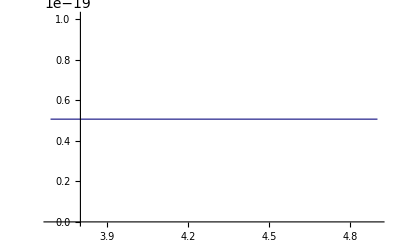

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

General::stop: 在本次计算中，Solve :: ifun 的进一步输出将被抑制.

-Graphics-

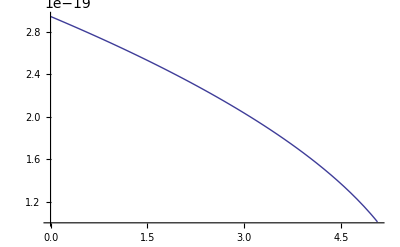

```mathematica
Plot[stepE01[VGS0,VDS,zmax[vbi,VGS0,VDS]],{z,zmax[vbi,VGS0,VDS],zmax[vbi,VGS0,VDS]+deltazRHS[VGS0,VDS,3]}]
Plot[E01z04[VGS0,VDS],{z,zmax[vbi,VGS0,VDS],zmax[vbi,VGS0,VDS]+deltazRHS[VGS0,VDS,3]}]
Plot[TFApprox04[VGS0,VDS,Ez],{Ez,0,Eq01[vbi,VGS0,VDS,zmax[vbi,VGS0,VDS]]}]
```

```mathematica
FlatVoltage = 
   FindRoot[Eq01[vbi, vgs, VDS, 0] == 
            Eq01[vbi, vgs, VDS, zmax[vbi, vgs, VDS]], {vgs, 0}][[1, 2]]
E01z01[vgs_, vds_] := E01[vbi, vgs, vds, deltazLHS[vgs, vds, 3]]
E01z02[vgs_, vds_] := E01[vbi, vgs, vds, 2 deltazLHS[vgs, vds, 3]]
E01z03[vgs_, vds_] := E01[vbi, vgs, vds, zmax[vbi, vgs, vds]]
E01z04[vgs_, vds_] := E01[vbi, vgs, vds, zmax[vbi, vgs, vds]]
E01z05[vgs_, vds_] := E01[vbi, vgs, vds, 4 deltazLHS[vgs, vds, 3]]
E01z06[vgs_, vds_] := E01[vbi, vgs, vds, 5 deltazLHS[vgs, vds, 3]]
TFApprox01[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z01[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 0, deltazLHS[vgs, vds, 3]}]], 0]
TFApprox02[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z02[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, deltazLHS[vgs, vds, 3], 2 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox03[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z03[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 2 deltazLHS[vgs, vds, 3], 3 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox04[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z04[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 3 deltazLHS[vgs, vds, 3], 4 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox05[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z05[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 4 deltazLHS[vgs, vds, 3], 5 deltazLHS[vgs, vds, 3]}]], 0]
TFApprox06[vgs_, vds_, Ez_] := If[vgs < FlatVoltage, Re[NIntegrate[Sqrt[E01z06[vgs, vds] - Ez - E01[vbi, vgs, vds, 0]], {z, 5 deltazLHS[vgs, vds, 3], 6 deltazLHS[vgs, vds, 3]}]], 0]
```

0.522891

```mathematica
0.514249
```

0.514249

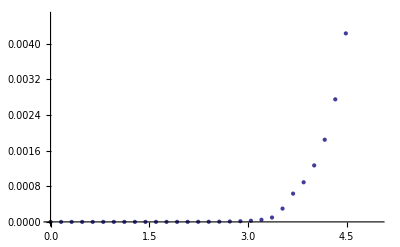

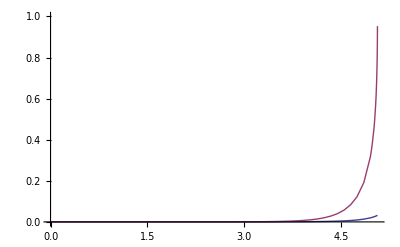

```mathematica
Show[ListPlot[Table[{Ez, Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]], 0.01 e}]], Plot[{Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {{0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, {0, 1}}]]
Plot[{Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]] Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TF[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {{0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, {0, 1}}]
```

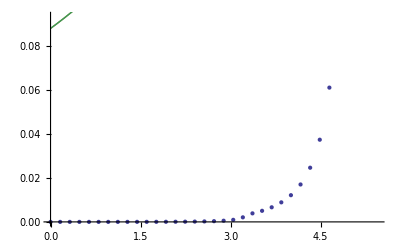

-Graphics-

```mathematica
NIntegrate::slwcon :  "Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/message/NIntegrate/slwcon\", ButtonNote -> \"NIntegrate::slwcon\"]\)"
```

Message::name: 消息名称 NIntegrate :: (slwcon : « 340 ») 不符合格式 symbol::name 或者 symbol::name::language.

NIntegrate::(slwcon:Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small. )

```mathematica
NIntegrate::ncvb :  "NIntegrate failed to converge to prescribed accuracy after \!\(9\) recursive bisections in \!\(z\) near \!\({z}\) = \!\({5.569582607143114`15.954589770191005*^-9}\). NIntegrate obtained \!\(1.044299386555847`*^-18 + \(\(3.2075695919549153`*^-21\\ ⅈ\)\)\) and \!\(7.429186200049437`*^-24\) for the integral and error estimates. \!\(\*ButtonBox[\"»\", ButtonStyle->\"Link\", ButtonFrame->None, ButtonData:>\"paclet:ref/message/NIntegrate/ncvb\", ButtonNote -> \"NIntegrate::ncvb\"]\)"
```

Message::name: 消息名称 NIntegrate :: (ncvb : « 495 ») 不符合格式 symbol::name 或者 symbol::name::language.

NIntegrate::(ncvb:NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {5.56958260714311×10^-9}. NIntegrate obtained 1.0443×10^-18 + 3.20757×10^-21\ ⅈ and 7.42919×10^-24 for the integral and error estimates. )

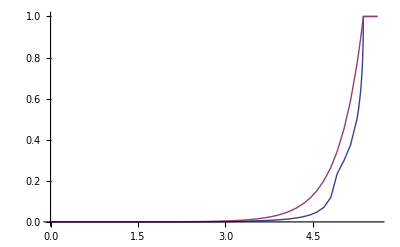

-Graphics-

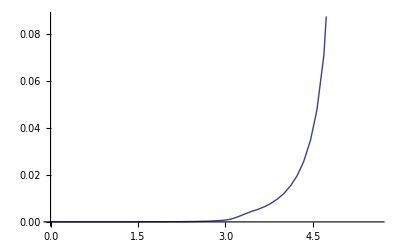

-Graphics-

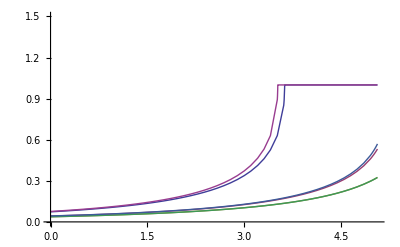

```mathematica
Plot[{Exp[-2/hbar Sqrt[2 mt] TFApprox01[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox02[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox03[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox04[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox05[VGS0, VDS, Ez]], Exp[-2/hbar Sqrt[2 mt] TFApprox06[VGS0, VDS, Ez]]}, {Ez, 0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {{0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, {0, 1.5}}]
```

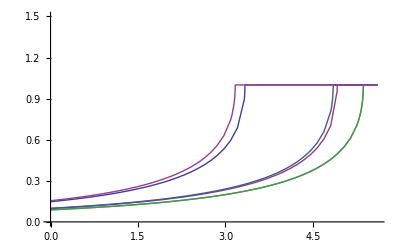

-Graphics-

## alternative approach of transition coefficient

### position of the lowest energy level in source

```mathematica
z01[vgs_,vds_,Ez_]:=Re[1/γ Log[C01]/.C01->(-(b3-Ez)-Sqrt[(b3-Ez)^2-4 b1 b2])/(2 b1)/.b1->a1+a2/.b2->a1-a2/.b3->E01VGS/.a1->η01/2 ugzero[vbi,vgs]/.a2->-(η01/2) ugzero[vbi,vgs]/Sinh[γ L] (Cosh[γ L]-ugLg[vbi,vgs,vds]/ugzero[vbi,vgs])/.η01->(subbandtable[[1,5]]+(4 π ϵsi)/Cox[R,Tox]) e/.E01VGS->-e WS+kB T subbandtable[[1,4]]/.WS->vgs-wgc+wfb]
z02[vgs_,vds_,Ez_]:=Re[1/γ Log[C02]/.C02->(-(b3-Ez)+Sqrt[(b3-Ez)^2-4 b1 b2])/(2 b1)/.b1->a1+a2/.b2->a1-a2/.b3->E01VGS/.a1->η01/2 ugzero[vbi,vgs]/.a2->-(η01/2) ugzero[vbi,vgs]/Sinh[γ L] (Cosh[γ L]-ugLg[vbi,vgs,vds]/ugzero[vbi,vgs])/.η01->(subbandtable[[1,5]]+(4 π ϵsi)/Cox[R,Tox]) e/.E01VGS->-e WS+kB T subbandtable[[1,4]]/.WS->vgs-wgc+wfb]
z01[VGS0,VDS,Eq01[vbi, VGS0, VDS, 0]](*SHOULD BE ELECTED*)
z02[VGS0,VDS,Eq01[vbi, VGS0, VDS, 0]]
```

7.32582×10^-9

-8.05061×10^-25

### slide the potential distribution into N pieces

#### difference between each piece

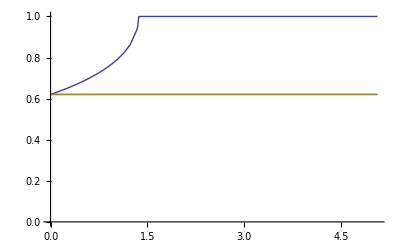

```mathematica
deltaz[vgs_,vds_,N_]:=z01[vgs,vds,Eq01[vbi, vgs,vds, 0]]/N
transcoef[vgs_,vds_,Ez_,N_,n_]:=If[vgs<FlatVoltage,Exp[-2/hbar Sqrt[2 mt] Re[Integrate[Sqrt[Eq01[vbi, vgs,vds,(n +1) deltaz[vgs,vds,N]]- Ez - E01[vbi, vgs, vds, 0]],{z,n deltaz[vgs,vds,N],(n+1) deltaz[vgs,vds,N]}]]],1]
Plot[{transcoef[VGS0,VDS,Ez,20,0],transcoef[VGS0,VDS,0,20,0],transcoef[VGS0,VDS,0,20,0]+Ez^2},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{0,1}]
```

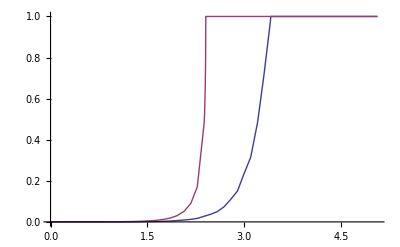

```mathematica
totaltransco[vgs_,vds_,Ez_,N_]:=Product[transcoef[vgs,vds,Ez,N,n],{n,0,20}]
Plot[{totaltransco[VGS2,VDS,Ez,20],Exp[-2/hbar Sqrt[2 mt] TF[VGS2, VDS, Ez]]},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{0,1}]
```

## total current

### tunel current

```mathematica
approxtunnelcurrentapprox[vgs_,vds_,st_]:=If[vgs<FlatVoltage,Re[e/(π hbar) st[[1,1]] NIntegrate[totaltransco[vgs,vds,Ez,20]/(1+Exp[(Eq01[vbi,vgs,vds,0]+Ez)/(kB T)]),{Ez,0,-Eq01[vbi,vgs,vds,0]+Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]}]],0]
Export["/home/tei/mathematica/anaertunnelcurrent_app.txt",Table[Re[{vgs,approxtunnelcurrentapprox[vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```

NIntegrate::ncvb: 在接近 {Ez} = {4.06508×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 8.45825×10^-26 和 2.12328×10^-30.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {Ez} = {4.93641×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.12373×10^-25 和 2.27685×10^-30.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {Ez} = {5.13425×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.49205×10^-25 和 3.75988×10^-30.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate :: slwcon 的进一步输出将被抑制.

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\anaertunnelcurrent_app.txt".

### total current

```mathematica
approxTatolCurrent[vgs_,vds_,st_]:=Re[1/(1+Exp[25(vgs-FlatVoltage+.2)]) approxtunnelcurrentapprox[vgs,vds,st]+1/(1+Exp[-25 (vgs-FlatVoltage+.2)]) DIBLSINGLEBANDCURRENT[vbi,vgs,vds,st]]
```

### plot

NIntegrate::ncvb: 在接近 {Ez} = {4.06491×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 8.46316×10^-26 和 2.11587×10^-30.

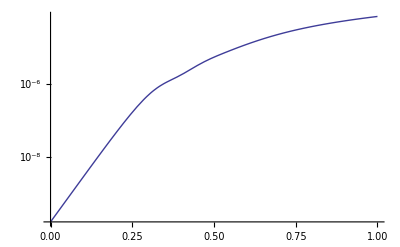

NIntegrate::ncvb: 在接近 {Ez} = {4.06491×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 8.46316×10^-26 和 2.11587×10^-30.

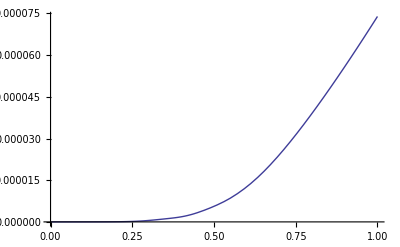

NIntegrate::ncvb: 在接近 {Ez} = {4.06508×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 8.45825×10^-26 和 2.12328×10^-30.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {Ez} = {4.93641×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.12373×10^-25 和 2.27685×10^-30.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {Ez} = {5.13425×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.49205×10^-25 和 3.75988×10^-30.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate :: slwcon 的进一步输出将被抑制.

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\anatotalcurrent.txt".

```mathematica
LogPlot[approxTatolCurrent[vgs,VDS,subbandtable],{vgs,0,1}]
Plot[approxTatolCurrent[vgs,VDS,subbandtable],{vgs,0,1}]
Export["/home/tei/mathematica/anatotalcurrent.txt",Table[Re[{vgs,approxTatolCurrent[vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```

NIntegrate::ncvb: 在接近 {Ez} = {4.06491×10^-20} 处的 Ez 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 8.46316×10^-26 和 2.11587×10^-30.

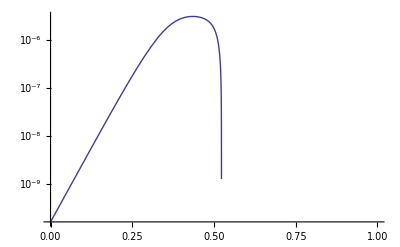

```mathematica
LogPlot[approxtunnelcurrentapprox[vgs,VDS,subbandtable],{vgs,0,1}]
```

```mathematica
Bi[vgs_,vds_,N_,n_]:=Sqrt[E01[vbi,vgs,vds,n deltaz[vgs,vds,N]]-E01[vbi,vgs,vds,0]]
```

## parabolic approximation of transmission coefficient

### transmission coefficient of each segment

#### segment factor

```mathematica
A[vgs_, vds_] := -2/hbar Sqrt[2 mt] (deltaz[vgs, vds, 20])
S[vgs_, vds_, n_] := 
 Sqrt[Eq01[vbi, vgs, vds, n deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]]

A[VGS0, VDS]
Sum[S[VGS0, VDS, m], {m, 1, N}] /. N -> 19
Sum[1/S[VGS0, VDS, m], {m, 1, 19}]
```

-4.08711×10^9

FactorSquareFree::lrgexp: 指数超出函数 FactorSquareFree 的界限.

General::stop: 在本次计算中，FactorSquareFree :: lrgexp 的进一步输出将被抑制.

3.84636×10^-9

9.86141×10^10

### approximation of root function of transmission expression

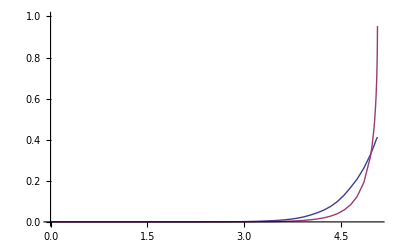

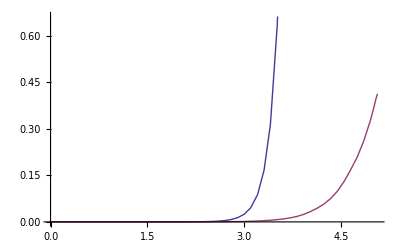

```mathematica
transcoef03[vgs_, vds_, Ez_, n_] := 
 If[Ez < Eq01[vbi, vgs, vds, (n + 1) deltaz[vgs, vds, 20]] - 
    E01[vbi, vgs, vds, 0], 
  Re[Exp[-2/hbar Sqrt[2 mt] deltaz[vgs, vds, 
      20] (Sqrt[
        Eq01[vbi, vgs, vds, (n + 1) deltaz[vgs, vds, 20]] - 
         E01[vbi, vgs, vds, 0]] - 
       Ez/(2 Sqrt[
           Eq01[vbi, vgs, vds, (n + 1) deltaz[vgs, vds, 20]] - 
            E01[vbi, vgs, vds, 0]]) - 
       0.5 Ez^2/ (Sqrt[
           Eq01[vbi, vgs, vds, (n + 1) deltaz[vgs, vds, 20]] - 
            E01[vbi, vgs, vds, 0]]^3))]], 1]
transmissioncoff[vgs_, vds_, Ez_] := 
 Product[transcoef03[vgs, vds, Ez, n], {n, 0, 20}]
Plot[{transmissioncoff[VGS0, VDS, Ez], 
  Exp[-2/hbar Sqrt[2 mt] TF[VGS0, VDS, Ez]], 
  totaltransco03[VGS0, VDS, Ez, 20]}, {Ez, 0, 
  Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}, PlotRange -> {0, 1}]

approxtotaltransco[vgs_, vds_, Ez_] := 
 Exp[-2/hbar Sqrt[2 mt] deltaz[vgs, vds, 
    20] (Sum[S[vgs, vds, m], {m, 1, 19}] - 
     Ez/2 Sum[1/S[vgs, vds, m], {m, 1, 19}] - 
     Ez^2/2 Sum[1/S[vgs, vds, m]^3, {m, 1, 19}])]
Plot[{approxtotaltransco[VGS0, VDS, Ez], 
  transmissioncoff[VGS0, VDS, Ez]}, {Ez, 0, 
  Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}]
```

## tunnel current

### parabolic approximation

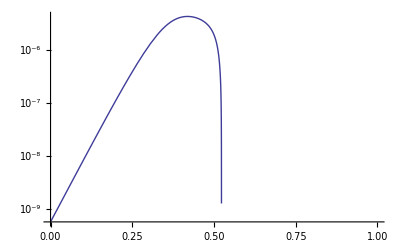

```mathematica
parabolicapproxtunnelcurrent[vgs_, vds_, st_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] NIntegrate[
     transmissioncoff[vgs, vds, 
       Ez]/(1 + Exp[(Eq01[vbi, vgs, vds, 0] + Ez)/(kB T)]), {Ez, 
      0, -Eq01[vbi, vgs, vds, 0] + 
       Eq01[vbi, vgs, vds, zmax[vbi, vgs, vds]]}]], 0]
LogPlot[parabolicapproxtunnelcurrent[vgs, VDS, subbandtable], {vgs, 0, 1}]
```

### current approximation(Boltzmman distribution)

```mathematica
(*partparabolicapproxitunnelcurrent[vgs_, vds_, st_, m_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar)
     st[[1, 1]] NIntegrate[
     Product[transcoef03[vgs, vds, Ez, i], {i, m, 
        20 - m}]/(Exp[(Eq01[vbi, vgs, vds, 0] + Ez)/(kB T)]), {Ez, 
      Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]], 
      Eq01[vbi, vgs, vds, (m + 1) deltaz[vgs, vds, 20]]}]] , 0]
partlayerparabolicapproxitunnelcurrent[vgs_, vds_, st_, i_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar)
     st[[1, 1]] NIntegrate[
     Exp[-2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) (Sum[S[vgs, vds, m], {m, i, 20 - i}] - 
          Ez/2 Sum[1/S[vgs, vds, m], {m, i, 20 - i}] - 
          Ez^2/2 Sum[1/S[vgs, vds, m]^3, {m, i, 20 - i}])]/(Exp[(Eq01[vbi, 
            vgs, vds, 0] + Ez)/(kB T)]), {Ez, 
      Eq01[vbi, vgs, vds, i deltaz[vgs, vds, 20]], 
      Eq01[vbi, vgs, vds, (i + 1) deltaz[vgs, vds, 20]]}]] , 0]
LogPlot[{Sum[
   partparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, m], {m, 1, 9}], 
  Sum[partlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i], {i, 
    1, 9}], parabolicapproxtunnelcurrent[vgs, VDS, subbandtable]}, {vgs, 0, 
  1}]*)
```

### current approximation using Error Function

```mathematica
(*equivpartlayerparabolicapproxitunnelcurrent[vgs_, vds_, st_, i_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar)
     st[[1, 1]] NIntegrate[
     Exp[-2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) (Sum[S[vgs, vds, m], {m, i, 20 - i}]+(Eq01[vbi, 
            vgs, vds, 0] )/(2/hbar Sqrt[
         2 mt] deltaz[vgs, vds, 20] kB T)- 
          Ez/2 (Sum[1/S[vgs, vds, m], {m, i, 20 - i}] -2/(2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) kB T))- 
          Ez^2/2 Sum[1/S[vgs, vds, m]^3, {m, i, 20 - i}])], {Ez, 
      Eq01[vbi, vgs, vds, i deltaz[vgs, vds, 20]], 
      Eq01[vbi, vgs, vds, (i + 1) deltaz[vgs, vds, 20]]}]] , 0]
Plot[{Sum[partlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i], {i, 
    1, 9}],Sum[equivpartlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}]},{vgs,0,1}]
LogPlot[{Sum[partlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i], {i, 
    1, 9}],Sum[equivpartlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}]},{vgs,0,1}]
```

```mathematica
(*errorpartparabolicapproxerftunnelcurrent[vgs_, vds_, st_, i_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] 1/
       2 Sqrt[π/c] Exp[
        a - (b)^2/(
         4 c)]] Erfi[(b+2 c)/(2 Sqrt[c]) (Eq01[vbi, vgs, vds, (i+1) deltaz[vgs, vds, 20]]-Eq01[vbi, vgs, vds, i deltaz[vgs, vds, 20]])]/. 
     a -> -2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (Sum[S[vgs, vds, m], {m, i, 20 - i}]+(Eq01[vbi, 
            vgs, vds, 0] )/(2/hbar Sqrt[
         2 mt] deltaz[vgs, vds, 20] kB T))/. 
    b -> 2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (0.5 Sum[1/S[vgs, vds, m], {m, i, 20 - i}] -1/(2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) kB T))/. 
   c ->2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (0.5 Sum[1/S[vgs, vds, m]^3, {m, i, 20 - i}]), 0]
partparabolicapproxerftunnelcurrent[vgs_, vds_, st_, i_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] 1/
       2 Sqrt[π/c] Exp[
        a - (b)^2/(
         4 c)]] (Erfi[1/(2 Sqrt[c])(b+2 c (Eq01[vbi, vgs, vds, (i+1) deltaz[vgs, vds, 20]])) ]-Erfi[1/(2 Sqrt[c])(b+2 c (Eq01[vbi, vgs, vds, i deltaz[vgs, vds, 20]])) ])/. 
     a -> -2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (Sum[S[vgs, vds, m], {m, i, 20 - i}]+(Eq01[vbi, 
            vgs, vds, 0] )/(2/hbar Sqrt[
         2 mt] deltaz[vgs, vds, 20] kB T))/. 
    b -> 2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (0.5 Sum[1/S[vgs, vds, m], {m, i, 20 - i}] -1/(2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) kB T))/. 
   c ->2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (0.5 Sum[1/S[vgs, vds, m]^3, {m, i, 20 - i}]), 0]
Plot[{Sum[errorpartparabolicapproxerftunnelcurrent[vgs, VDS, subbandtable, i], {i, 
   1, 9}],Sum[equivpartlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}],Sum[partparabolicapproxerftunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}]}, {vgs, 0, 1}]
LogPlot[{Sum[errorpartparabolicapproxerftunnelcurrent[vgs, VDS, subbandtable, i], {i, 
   1, 9}],Sum[equivpartlayerparabolicapproxitunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}],Sum[partparabolicapproxerftunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}]}, {vgs, 0, 1}]
```

```mathematica
partparabolicapproxerftunnelcurrent[VGS0, VDS, subbandtable, 9]
```

1.28852×10^-11

```mathematica
TraditionalForm[Integrate[Exp[a+b x+c x^2],x]]
```

(√π ⅇ^(a-b^2/(4 c)) erfi((b+2 c x)/(2 √c)))/(2 √c)

```mathematica
Integrate[Exp[a+b x+c x^2],x]
```

(ⅇ^(a-b^2/(4 c)) √π Erfi[(b+2 c x)/(2 √c)])/(2 √c)

```mathematica
Export["/home/tei/mathematica/errorpartparabolicapproxerftunnelcurrent.txt",Table[Re[{vgs,Sum[errorpartparabolicapproxerftunnelcurrent[vgs, VDS, subbandtable, i], {i, 
   1, 9}]}],{vgs,0,1,0.01}],"CSV"];
```

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\errorpartparabolicapproxerftunnelcurrent.txt".

```mathematica
Export["/home/tei/mathematica/partparabolicapproxerftunnelcurrent.txt",Table[Re[{vgs,Sum[partparabolicapproxerftunnelcurrent[vgs, VDS, subbandtable, i], {i, 
   1, 9}]}],{vgs,0,1,0.01}],"CSV"];
```

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\partparabolicapproxerftunnelcurrent.txt".

## using taylor expansion at barrier top

### definition of 2nd order taylor expansion

```mathematica
(*F[Ez_,vgs_,vds_,n_,β_,α_,χ_]:=Sqrt[a-β a]-1/(α Sqrt[a-β a]) (Ez-β a)-1/(χ (Sqrt[a-β a])^3) (Ez-β a)^2/.a->Eq01[vbi, vgs, vds, n deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]
Plot[F[Ez,VGS0,VDS,1,0.9,100,1000],{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]}]
```

```mathematica
(*contrastf[vgs_,vds_,n_,Ez_]:=Sqrt[Eq01[vbi, vgs, vds, n deltaz[vgs, vds, 20]] -Ez- E01[vbi, vgs, vds, 0]]
Plot[{contrastf[VGS0,VDS,1,Ez],F[Ez,VGS0,VDS,1,0.8,15/14,15],Sqrt[Eq01[vbi, VGS0, VDS,deltaz[VGS0, VDS, 20]]- Eq01[vbi, VGS0, VDS, 0]],Sqrt[Eq01[vbi, VGS0,VDS,deltaz[VGS0,VDS,20]]- E01[vbi,VGS0,VDS,0]]- Ez/(2 Sqrt[Eq01[vbi,VGS0,VDS,(0+1) deltaz[VGS0,VDS,20]]- E01[vbi, VGS0,VDS,0]])-Ez^2/ (2 Sqrt[Eq01[vbi,VGS0,VDS,(0+1) deltaz[VGS0,VDS,20]]- E01[vbi, VGS0,VDS,0]]^3)},{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{{0. Eq01[vbi, VGS0, VDS,zmax[vbi, VGS0, VDS]]},{0,5.5 10^-10}}]
Export["E:\data_for_mathematica\\sqrtcontentTC.txt",Table[Re[{Ez,contrastf[VGS0,VDS,1,Ez]}],{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]- E01[vbi, VGS0, VDS, 0],0.001 e}],"CSV"];
Export["E:\data_for_mathematica\\sqrtcontentTEapproxselectedpointTC.txt",Table[Re[{Ez,F[Ez,VGS0,VDS,1,0.9,10,10/9]}],{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]- E01[vbi, VGS0, VDS, 0],0.001 e}],"CSV"];
Export["E:\data_for_mathematica\\sqrtcontentTEapproxzeropointTC.txt",Table[Re[{Ez,Sqrt[Eq01[vbi, VGS0,VDS,deltaz[VGS0,VDS,20]]- E01[vbi,VGS0,VDS,0]]- Ez/(2 Sqrt[Eq01[vbi,VGS0,VDS,(0+1) deltaz[VGS0,VDS,20]]- E01[vbi, VGS0,VDS,0]])-0.5Ez^2/ (Sqrt[Eq01[vbi,VGS0,VDS,(0+1) deltaz[VGS0,VDS,20]]- E01[vbi, VGS0,VDS,0]]^3)}],{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]- E01[vbi, VGS0, VDS, 0],0.01 e}],"CSV"];
```

```mathematica
(*Eq01[vbi,VGS0,VDS, 1 deltaz[VGS0,VDS, 20]] - E01[vbi, VGS0,VDS, 0]
Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]- E01[vbi, VGS0, VDS, 0]
```

```mathematica
(*V[vgs_,vds_,z_,Ez_]:=E01[vbi,vgs,vds,z]-E01[vbi,vgs,vds,0]-Ez
TF[vgs_,vds_,Ez_]:=Re[NIntegrate[Sqrt[V[vgs,vds,z,Ez]],{z,z02[vgs,vds,Ez],z01[vgs,vds,Ez]}]]
```

```mathematica
(*transcoef10[vgs_,vds_,Ez_,n_]:=If[Ez<Eq01[vbi, vgs,vds,n  deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0],Re[Exp[-2/hbar Sqrt[2 mt] deltaz[vgs,vds,20] (contrastf[vgs,vds,n,Ez])]],1]
transcoef11[vgs_,vds_,Ez_,n_]:=If[Ez<Eq01[vbi, vgs,vds,n  deltaz[vgs,vds,20]]- E01[vbi, vgs, vds, 0],Re[Exp[-2/hbar Sqrt[2 mt] deltaz[vgs,vds,20] (F[Ez,vgs,vds,n,0.9,15,15/14])]],1] 
Plot[{Product[transcoef10[VGS2,VDS,Ez,m],{m,1,19}],Product[transcoef11[VGS2,VDS,Ez,m],{m,1,19}],Exp[-2/hbar Sqrt[2 mt] TF[VGS2,VDS,Ez]](*,Exp[-2/hbar Sqrt[2 mt] TF[VGS0, VDS, Ez]]*)},{Ez,0, Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]-Eq01[vbi, VGS0, VDS, 0]},PlotRange->{0,1}]
Export["E:\data_for_mathematica\\totalF.txt",Table[Re[{Ez,Product[transcoef10[VGS0,VDS,Ez,m],{m,1,19}]}],{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]+Eq01[vbi, VGS0, VDS, 0],0.01 e}],"CSV"];
Export["E:\data_for_mathematica\\totalFelectedpoint.txt",Table[Re[{Ez,Product[transcoef11[VGS0,VDS,Ez,m],{m,1,19}]}],{Ez,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]+Eq01[vbi, VGS0, VDS, 0],0.01 e}],"CSV"];
```

```mathematica
(*numtunnelcurrent[vgs_,vds_,st_]:=If[vgs<FlatVoltage,Re[e/(π hbar) st[[1,1]] NIntegrate[Exp[-2/hbar Sqrt[2 mt] TF[vgs,vds,Ez]]/(1+Exp[(Eq01[vbi,vgs,vds,0]+Ez)/(kB T)]),{Ez,0,-Eq01[vbi,vgs,vds,0]+Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]}]],0]
halfTEtunnelcurrent[vgs_, vds_, st_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] NIntegrate[
     Product[transcoef11[vgs,vds,Ez,m],{m,1,19}]/(Exp[(Eq01[vbi, vgs, vds, 0] + Ez)/(kB T)]), {Ez,0, -Eq01[vbi, vgs, vds, 0]+Eq01[vbi, vgs, vds, zmax[vbi, vgs, vds]]}]], 0]
LogPlot[{halfTEtunnelcurrent[vgs, VDS, subbandtable],parabolicapproxtunnelcurrent[vgs, VDS, subbandtable],numtunnelcurrent[vgs,VDS,subbandtable]}, {vgs, 0, 1}]
Export["E:\data_for_mathematica\\halfTEtnnelcurrent.txt",Table[Re[{vgs,halfTEtunnelcurrent[vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"]
```

```mathematica
(*BTTEerftunnelcurrent[vgs_, vds_, st_, i_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] 1/
       2 Sqrt[π/c] Exp[
        a - (b)^2/(
         4 c)]] (Erfi[1/(2 Sqrt[c])(b+2 c (Eq01[vbi, vgs, vds, (i+1) deltaz[vgs, vds, 20]])) ]-Erfi[1/(2 Sqrt[c])(b+2 c (Eq01[vbi, vgs, vds, i deltaz[vgs, vds, 20]])) ])/. 
     a -> -2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (Sum[Sqrt[0.1 Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]]+1/(10 Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])(0.9 Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0])-0.9^2 (Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0])^2/(10/9 (Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3), {m, i, 20 - i}]+(Eq01[vbi, 
            vgs, vds, 0] )/(2/hbar Sqrt[
         2 mt] deltaz[vgs, vds, 20] kB T))/. 
    b -> 2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (Sum[1/(10 Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])-1/(10/9 (Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3) 2 0.9 (Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]) ,{m,i,20-i}]-1/(2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) kB T))/. 
   c ->2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] Sum[(1/ ((10/9) Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3), {m, i, 20 - i}], 0]
Plot[Sum[BTTEerftunnelcurrent[vgs, VDS, subbandtable, i],{i,1,9}], {vgs, 0, 1}]
```

```mathematica
(*Solve[F[α,VGS0,VDS,2,0.999,a,b]==0 && F[0,VGS0,VDS,2,0.999,a,b]==Sqrt[α]/.α->Eq01[vbi, VGS0, VDS, (1+1) deltaz[VGS0, VDS, 20]]-Eq01[vbi, VGS0, VDS, 0],{a,b}]
```

```mathematica
(*Solve[1/a+1/b==1 && F[0,VGS0,VDS,2,0.999,a,b]==Sqrt[α]/.α->Eq01[vbi, VGS0, VDS, (2) deltaz[VGS0, VDS, 20]]-Eq01[vbi, VGS0, VDS, 0],{a,b}]
```

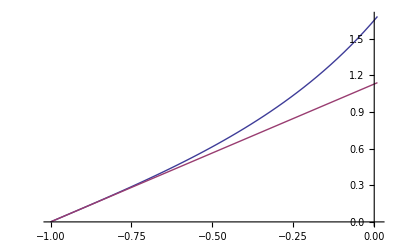

```mathematica
Plot[{Erfi[1+x],(2 (1+x))/(√π)},{x,-1,0.01}]
```

```mathematica
Series[Erfi[x],{x,0,10}]
```

(2 x)/(√π)+(2 x^3)/(3 √π)+x^5/(5 √π)+x^7/(21 √π)+x^9/(108 √π)+O[x]^11

```mathematica
(*FF[vgs_, vds_,  x_,i_]:=Re[Erfi[1/(2 Sqrt[c])(b+2 c (x)) ]]/. 
    b -> 2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (Sum[1/(10 Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])-1/(10/9 (Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3) 2 0.9 (Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]) ,{m,i,20-i}]-1/(2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) kB T))/. 
   c ->2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] Sum[(1/ ((10/9) Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3), {m, i, 20 - i}]
GG[vgs_, vds_,  x_,i_]:=Re[2/Sqrt[π] (1/(2 Sqrt[c])(b+2 c (x)) )]/. 
    b -> 2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] (Sum[1/(10 Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])-1/(10/9 (Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3) 2 0.9 (Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]) ,{m,i,20-i}]-1/(2/hbar Sqrt[
         2 mt] (deltaz[vgs, vds, 20]) kB T))/. 
   c ->2/hbar Sqrt[2 mt] deltaz[vgs, vds, 20] Sum[(1/ ((10/9) Sqrt[(0.1) Eq01[vbi, vgs, vds, m deltaz[vgs, vds, 20]] - E01[vbi, vgs, vds, 0]])^3), {m, i, 20 - i}]
Plot[{FF[VGS0,VDS,x,1],GG[VGS0,VDS,x,1]},{x,0,Eq01[vbi, VGS0, VDS, zmax[vbi, VGS0, VDS]]},PlotRange->{0,0.2}]
```

## parabolic potential approximation transmition coefficient

### parabolic potential

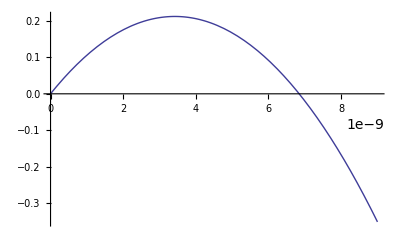

```mathematica
PEnergy[vgs_,vds_,z_]:=-a (z-zmax[vbi,vgs,vds])^2+c/.a->(Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]-Eq01[vbi,vgs,vds,0])/zmax[vbi,vgs,vds]^2/.c->Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]-Eq01[vbi,vgs,vds,0]
Plot[PEnergy[VGS2,VDS,z]/e,{z,0,L}]
Export["E:\data_for_mathematica\\paraboenergyVgs00vds06.txt",Table[Re[{10^9 z,PEnergy[VGS0,VDS,z]/e}],{z,0,L,0.05 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboenergyVgs02vds06.txt",Table[Re[{10^9 z,PEnergy[VGS2,VDS,z]/e}],{z,0,L,0.05 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboenergyVgs05vds06.txt",Table[Re[{10^9 z,PEnergy[VGS5,VDS,z]/e}],{z,0,L,0.05 nm}],"CSV"];
```

### transmition coeffeicient

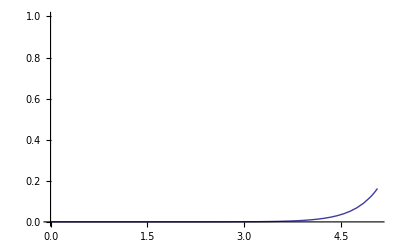

```mathematica
parabolictranscoe[vgs_,vds_,Ez_]:=If[vgs < FlatVoltage,Exp[-π/hbar Sqrt[(2 mt)/a] (Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]-Ez-Eq01[vbi,vgs,vds,0])]/.a->(Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]-Eq01[vbi,vgs,vds,0])/zmax[vbi,vgs,vds]^2,1]
Plot[parabolictranscoe[VGS0,VDS,Ez],{Ez,0,Eq01[vbi,VGS0,VDS,zmax[vbi,VGS0,VDS]]},PlotRange->{0,1}]
```

### tunnel current

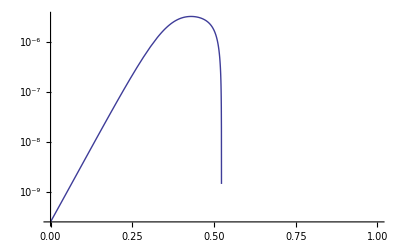

```mathematica
parabolicapproxtunnelcurrent[vgs_, vds_, st_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] NIntegrate[
     parabolictranscoe[vgs, vds, 
       Ez]/(1 + Exp[(Eq01[vbi, vgs, vds, 0] + Ez)/(kB T)]), {Ez, 
      0, -Eq01[vbi, vgs, vds, 0] + 
       Eq01[vbi, vgs, vds, zmax[vbi, vgs, vds]]}]], 0]
LogPlot[parabolicapproxtunnelcurrent[vgs, VDS, subbandtable], {vgs, 0, 1}]
```

### approximation of tunneling current

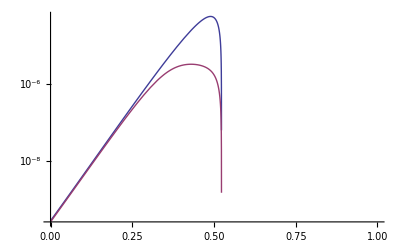

```mathematica
approxtparabolicunnelcurrent[vgs_, vds_, st_] := 
 If[vgs < FlatVoltage, 
  Re[e/(π hbar) st[[1, 1]] Exp[a]/b (Exp[b (Eq01[vbi, vgs, vds, zmax[vbi, vgs, vds]]-Eq01[vbi, vgs, vds, 0])]-Exp[b 0])/.a->-π/hbar Sqrt[2 mt/c]  Eq01[vbi, vgs, vds, zmax[vbi, vgs, vds]]+(π/hbar Sqrt[2 mt/c]-1/(kB T)) Eq01[vbi, vgs, vds, 0]]/.b->π/hbar Sqrt[2 mt/c]-1/(kB T)/.c->(Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]-Eq01[vbi,vgs,vds,0])/zmax[vbi,vgs,vds]^2, 0]
LogPlot[{approxtparabolicunnelcurrent[vgs, VDS, subbandtable],parabolicapproxtunnelcurrent[vgs, VDS, subbandtable]}, {vgs, 0, 1}]
Export["E:\data_for_mathematica\\approxtparabolicunnelcurrent.txt",Table[Re[{vgs,approxtparabolicunnelcurrent[vgs,VDS,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```

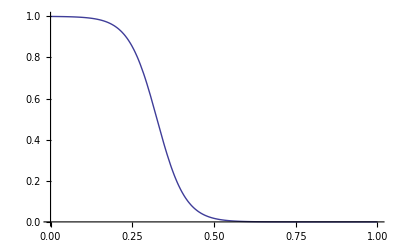

```mathematica
SF[vgs_]:=(1+Exp[μ ((e (vgs-wgc+wfb))/(kB T)-subbandtable[[1,4]]-ν)])^-1/.μ->0.6/.ν->-4.5
Plot[SF[vgs],{vgs,0,1}]
U[vgs_]:=b/(2 a) (-1+Sqrt[1+(4 a)/(b b) 1/25 Log[1+Exp[25 (vgs+c)]]])/.a->(8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1,1]]^2 e^3 mt)/.b->subbandtable[[1,5]]+(4 Pi ϵsi)/(Cox[R,Tox])/.c->-wgc+wfb-subbandtable[[1,3]]
```

## Finger shape transmition coefficient

### definition of transmition coefficient

```mathematica
fingertranscoef[vgs_, vds_, Ez_, n_] := 
 If[Ez < Eq01[vbi, vgs, vds, (n + 1) deltaz[vgs, vds, 20]] - 
    E01[vbi, vgs, vds, 0], 
  Re[Exp[-π/hbar Sqrt[2 mt/a] (c-Ez)]]/.a->(4 (Eq01[vbi,vgs,vds,(n + 1) deltaz[vgs, vds, 20]]-Eq01[vbi,vgs,vds,0]))/deltaz[vgs, vds, 20]^2/.c->Eq01[vbi,vgs,vds,(n + 1) deltaz[vgs, vds, 20]]-Eq01[vbi,vgs,vds,0], 1]
```

## total current

```mathematica
WITHOUTDIBLSINGLEBANDCURRENT[vgs_,vds_,r_,tox_,st_]:=Re[(e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi U[vgs])/Cox[R,Tox])-st[[1,4]]-st[[1,5]]/vt U[vgs]]]-Log[1+Exp[1/vt (vgs-wgc+wfb-(4 Pi ϵsi U[vgs])/Cox[R,Tox])-st[[1,4]]-st[[1,5]]/vt U[vgs]-vds/vt]])]
```

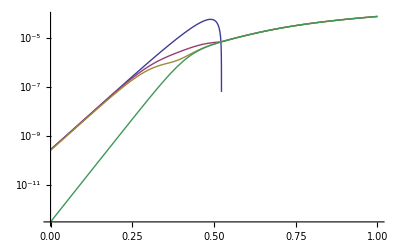

```mathematica
numtotalcurrent[vgs_,vds_,r_,tox_,st_]:=parabolicapproxtunnelcurrent[vgs, VDS, subbandtable] SF[vgs]+WITHOUTDIBLSINGLEBANDCURRENT[vgs,vds,r,tox,st]
totalcurent[vgs_,vds_,r_,tox_,st_]:=approxtparabolicunnelcurrent[vgs, VDS, subbandtable] SF[vgs]+WITHOUTDIBLSINGLEBANDCURRENT[vgs,vds,r,tox,st]
LogPlot[{approxtparabolicunnelcurrent[vgs, VDS, subbandtable],totalcurent[vgs,VDS,R,Tox,subbandtable],numtotalcurrent[vgs,VDS,R,Tox,subbandtable],WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable]},{vgs,0,1}]
Export["E:\data_for_mathematica\approxtparabolicunnelcurrent.txt",Table[Re[{vgs,approxtparabolicunnelcurrent[vgs, VDS, subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["E:\data_for_mathematica\approxtparabolicunnelcurrent_ua.txt",Table[Re[{vgs,10^6 approxtparabolicunnelcurrent[vgs, VDS, subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["E:\data_for_mathematica\\totalcurent.txt",Table[Re[{vgs,totalcurent[vgs,VDS,R,Tox,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["E:\data_for_mathematica\\totalcurent_ua.txt",Table[Re[{vgs,10^6 totalcurent[vgs,VDS,R,Tox,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["E:\data_for_mathematica\WITHOUTDIBLSINGLEBANDCURRENT.txt",Table[Re[{vgs,WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
Export["E:\data_for_mathematica\WITHOUTDIBLSINGLEBANDCURRENT_ua.txt",Table[Re[{vgs,10^6 WITHOUTDIBLSINGLEBANDCURRENT[vgs,VDS,R,Tox,subbandtable]}],{vgs,0,1,0.01}],"CSV"];
```